## Conventional poverty trap (physical capital)

dk_P/dt=s(k_P)f(k_P)-(δ_P+n)k_P

f(k_P)=Ak_P^α_1
s(k_P) = s_1+ (s_2-s_1)/(1+ⅇ^(-s_3(k_P-d)))
k_P: physical capital
f(k_P): standard neoclassical production function
s(k_P): savings rate from initial value s_1 up to s_2 at k_P=d
δ_P: depreciation rate physical capital
n: population growth rate
A: technology

{0.,1.00008,2.00769,3.17478}

print[{0.,1.00008,2.00769,3.17478}]

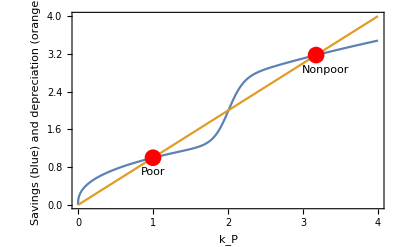

```mathematica
A=10;
α1=Rationalize[0.4];
s1=Rationalize[0.1];
s2=Rationalize[0.2];
s3=10;
d=2;
δP=Rationalize[0.5];
n=Rationalize[0.5];
f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
Savings:=sf[kP] f[kP]
Depreciation:=(δP+n) kP

(* Find equilibrium points *)
kPEq=NSolve[Savings==Depreciation && 0 ≤kP≤4,kP];
kPList=kP/.%
yValues={};
Do[AppendTo[yValues,sf[i] f[i]],{i,kPList}]
print[yValues]

(* Plot conventional poverty trap and equilibrium points *)
data:={{1.00008,1.00008},{3.174781185869739,3.174781185869739}};
p1=Plot[{Savings,Depreciation}, {kP,0,4}, 
Frame->True, FrameLabel->{"k_P", "Savings (blue) and depreciation (orange)"}];
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Style[Text["Poor",{1,0.7}],Bold],Style[Text["Nonpoor",{3.3,2.85}],Bold]}];
Show[{p1,p2,p3}]
```

## Physical and natural capital

dk_P/dt=s(k_P)E(K_N)f(k_P)-(δ_P+n)k_P
dK_N/dt = G(K_N)L(k_P)-δ_N K_N

E(K_N) = qK_N^α_2
G(K_N) = bK_N^2/(H^2+K_N^2)
L(k_P) = 1/(1+c_1 k_P^2)

K_N: natural capital
E(K_N): function representing the contributions of natural capital to production
G(K_N): natural capital growth function
L(k_P): reduction in growth of natural capital due to physical capital

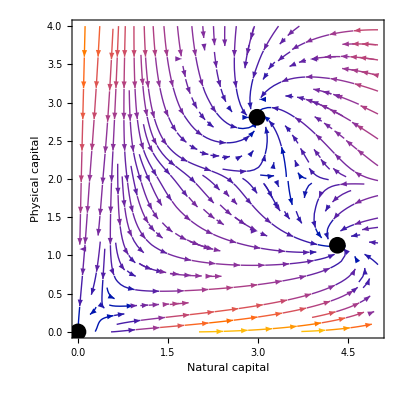

-Graphics-

```mathematica
A=10;
α1=Rationalize[0.4];
s1=Rationalize[0.1];
s2=Rationalize[0.2];
s3=10;
d=2;
δP=Rationalize[0.5];
n=Rationalize[0.5];
α2 = Rationalize[0.4];
δN = 1;
b=10;
H=Rationalize[1.5];
c1=1;
c2=Rationalize[0.5];
q=Rationalize[0.6];

f[kP_]:=A kP^α1;
sf[kP_]:=s1+(s2-s1)/(1+ⅇ^(-s3 (kP-d)));
Ef[KN_]:=q KN^α2
G[KN_]:=(b KN^2)/(H^2+KN^2)
L[kP_]:=1/(1+c1 kP^c2)

dkPdt:=sf[kP] Ef[KN] f[kP]-(δP+n) kP
dKNdt:=G[KN] L[kP]-δN KN

(* Streamplot *)
p1=StreamPlot[{dKNdt,dkPdt},{KN,0,5},{kP,0,4}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}];
data:={{0,0},{4.32345,1.13309},{2.98333,2.80753}};
p2=Graphics[{Black,PointSize[0.03],Point[data]}];
Show[{p1,p2}]

(* Plot basin of attractions *)
tEnd=25;
kPmin=0;
kPmax=4;
KNmin=0;
KNmax=5;
stepsize=0.01;

ListIndices={};
Do[AppendTo[ListIndices,{i,j}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize}]
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5},
sol=NDSolveValue[{kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==((b*(KN[t])^2)/(H^2+(KN[t])^2))*(1/(1+c1*kP[t]^c2))-δN*KN[t],
kP[0]==i,KN[0]==j},{kP[tEnd],KN[tEnd]},{t,0,tEnd},AccuracyGoal->30];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,Automatic,1];
CountDistinct[AssignClusters];
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[n]]==3,AppendTo[cluster3,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]
p1=ListPlot[{Reverse[cluster1,2],Reverse[cluster2,2],Reverse[cluster3,2]},Frame->True, PlotStyle->PointSize[0.005],FrameLabel->{"K_N","k_P"}];
data:={{0,0},{4.32345,1.13309},{2.98333,2.80753}};
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Text[Style["Poor and degraded",Bold],{0.2,1.8},Automatic, {0,1}],Text[Style["Poor",Bold],{4.3,0.8}],Text[Style["Intermediate",Bold],{3,3.1}]}];
Show[{p1,p2, p3}]
```

## Physical, natural and cultural capital

dk_P/dt=s(k_P)E(K_N)f(k_P)-(δ_P+n)k_P
dK_N/dt = T(K_C)G(K_N)L(k_P)-δ_N K_N
dK_C/dt=P(K_N)-δ_C K_C

P(K_N) = (P_0 K_N)/(P_N+K_N)
T(K_C) = T_0 K_C

K_C: cultural capital
δ_C: depreciation rate of cultural capital
P(K_N): practice of traditional activities
T(K_C): effect of cultural capital on growth of natural capital

```mathematica
tEnd=24;
kPmin=0;
kPmax=5;
KNmin=0;
KNmax=5;
KCmin=0;
KCmax=5;
stepsize=0.1;

ListIndices={};
Do[AppendTo[ListIndices,{i,j,k}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5},
sol=NDSolveValue[{kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(1/(1+c1*(kP[t])^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))-δC*KC[t],
kP[0]==i,KN[0]==j,KC[0]==k},{kP[tEnd],KN[tEnd],KC[tEnd]},{t,0,tEnd}];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,3,1];
CountDistinct[AssignClusters]
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[n]]==3,AppendTo[cluster3,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]

(* Plot with dots*)
ListPointPlot3D[{cluster3,{{1.0,3.4,2.3},{0,0,0}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{1,1,1},
PlotStyle->{Opacity[1],PointSize[0.05]}]

(* Surface plot*)
cluster3=Reverse[cluster3,2];
cluster3=Reverse[cluster3,1];
data2:={{2.3,3.4,1.0},{0,0,0}};
p1=ListPlot3D[{cluster3,cluster2},PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},AxesLabel->{"K_C","K_N","k_P"},BoxRatios->{1,1,1},InterpolationOrder->3,Mesh->None,PlotStyle->{Opacity[0.2],PointSize[0.05]}];
p2=Graphics3D[{Red,PointSize[0.05],Point[data2]},PlotRange->{{KCmin,KCmax},{KNmin,KNmax},{kPmin,kPmax}}];
p3 = Graphics3D[{Text[Style["Intermediate ",Bold],{1,1.5,2}],Text[Style["Poor and degraded ",Bold],{0.5,1.5,0}]}];
Show[{p1,p2,p3}]
```

3

-Graphics3D-

-Graphics3D-

## Intensification trap model after transformation

dk_P/dt=s(k_P)E(K_N)f(k_P)-(δ_P+n)k_P
dK_N/dt = T(K_C)G(K_N)L_2(k_P)-δ_N K_N
dK_C/dt=P(K_N)-δ_C K_C

L_2(k_P) = ρ + (1-ρ)/(1+c_1 k_P^c_2)

```mathematica
tEnd=24;
kPmin=0;
kPmax=5;
KNmin=0;
KNmax=10;
KCmin=0;
KCmax=5;
stepsize=0.1;

ListIndices={};
Do[AppendTo[ListIndices,{i,j,k}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5},
sol=NDSolveValue[{kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))-δC*KC[t],
kP[0]==i,KN[0]==j,KC[0]==k},{kP[tEnd],KN[tEnd],KC[tEnd]},{t,0,tEnd}];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,Automatic,1];
CountDistinct[AssignClusters]
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[n]]==3,AppendTo[cluster3,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]

(* Plot with dots *)
ListPointPlot3D[{cluster1,{{0,0,0},{4.6,6.2,2.9}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{1,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]

(* Surface plot *)
data:={{4.6,2.9,6.2},{0,0,0}};
Do[AppendTo[cluster1[[i]],cluster1[[i]][[2]]],{i,1,Length[cluster1]}];
cluster1=Reverse[Drop[cluster1,None,{2}]];
p1=ListPlot3D[{cluster1},Filling->Bottom,FillingStyle->"Ambient", PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KNmin,KNmax}},AxesLabel->{"K_C","K_N","k_P"},BoxRatios->{1,1,2},InterpolationOrder->3,Mesh->None,PlotStyle->{Opacity[0.2],PointSize[0.05]}];
p2=Graphics3D[{Red,PointSize[0.05],Point[data]},PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KNmin,KNmax}}];
p3 = Graphics3D[{Text[Style["Nonpoor",Bold],{4,2,6.5}],Text[Style["Poor and degraded",Bold],{2.5,1.5,1}]}];
Show[{p1,p2,p3}]
```

4

-Graphics3D-

-Graphics3D-

## Subsistence trap model

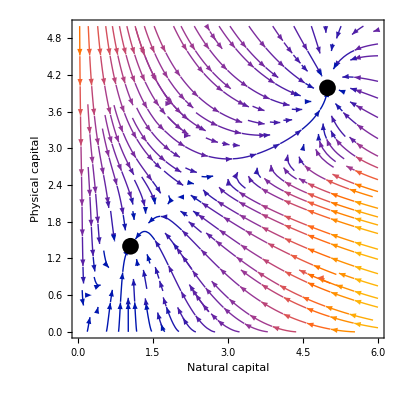

-Graphics-

```mathematica
s=0.2;
A=10;
q=0.6;
α1=0.4;
α2=0.4;
δP=0.5;
n=0.5;
r=0.2;
K=5;
D0=0.8;
D1=4;
D2=2.5;

f[kP_]:=A kP^α1;
Ef[KN_]:=q KN^α2;
G2[KN_]=r KN (K-KN);
Df[kP_]=D0/(1+ⅇ^(D1 (kP-D2)));

dkPdt:=s f[kP] Ef[KN]-(δP+n) kP
dKNdt:=G2[KN]-KN Df[kP]

p1=StreamPlot[{dKNdt,dkPdt},{KN,0,6},{kP,0,5}, 
Frame->True, FrameLabel->{"Natural capital", "Physical capital"}];
data:={{1.05,1.4},{4.99,3.99}};
p2=Graphics[{Black,PointSize[0.03],Point[data]}];
Show[{p1,p2}]

(* Plot basin of attractions *)

tEnd=100;
kPmin=0;
kPmax=5;
KNmin=0;
KNmax=6;
stepsize=0.01;

ListIndices={};
Do[AppendTo[ListIndices,{i,j}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize}]
ListSol={};
Do[
With[{s=0.2,A=10,q=0.6,α1=0.4,α2=0.4,δP=0.5,δN = 1,n=0.5,r=0.2,K=5,D0=0.8,D1=4,D2=2.5},
sol=NDSolveValue[{kP'[t]==s*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(r KN[t] (K-KN[t]))-KN[t]*(D0/(1+ⅇ^(D1 (kP[t]-D2)))),
kP[0]==i,KN[0]==j},{kP[tEnd],KN[tEnd]},{t,0,tEnd},AccuracyGoal->40];
AppendTo[ListSol,Threshold[sol,10^-5]]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,Automatic,1];
CountDistinct[AssignClusters];
cluster1={};
Do[If[AssignClusters[[l]]==1,AppendTo[cluster1,ListIndices[[l]]]],{l,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[m]]==2,AppendTo[cluster2,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
p1=ListPlot[{Reverse[cluster1,2],Reverse[cluster2,2]},PlotMarkers->"■",PlotStyle->PointSize[0.01],Frame->True, FrameLabel->{"Natural capital", "Physical capital"}];
data:={{1.05,1.4},{4.99,3.99}};
p2=Graphics[{Red,PointSize[0.03],Point[data]}];
p3=Graphics[{Style[Text[Poor,{1,1}],Bold],Style[Text[Nonpoor,{4.99,3.5}],Bold]}];
Show[{p1,p2, p3}]
```

## Intensification trap model after transformation + social capital

dk_P/dt=s(k_P)E(K_N)f(k_P)-(δ_P+n)k_P
dK_N/dt = T(K_C)G(K_N)L_2(k_P)-δ_N K_N
dK_C/dt=P(K_N)M(K_S)-δ_C K_C
dK_S/dt = I(K_S)J(K_C)-δ_SK_S

K_S = social capital
δ_S=loss of cultural capital
I(K_S) = growth of social capital
J(K_C) = increase in growth of social capital due to cultural capital
M(K_S) = increase in growth of cultural capital due to social capital

I(K_S) = I_0 K_S(I_1-K_S)		(logistic function)
J(K_C) = K_C^J_0
M(K_S) = K_S^M_0

{{kP→InterpolatingFunction[…],KN→InterpolatingFunction[…],KC→InterpolatingFunction[…],KS→InterpolatingFunction[…]}}

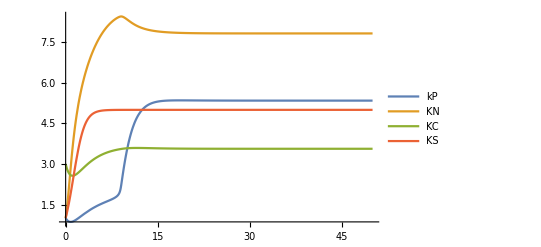

{{5.34158,7.8262,3.56096,5.}}

```mathematica
(*Results for one set of initial conditions over time *)
tEnd=50;

With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5,I0=0.2,I1=5,J0=0.1,M0=0.1,δS=0.0},
sol=NDSolve[{
kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))*(KS[t]^M0)-δC*KC[t],
KS'[t]==(I0*KS[t]*(I1-KS[t]))*(KC[t]^J0)-δS*KS[t],
kP[0]==1,KN[0]==1,KC[0]==3,KS[0]==1},{kP,KN,KC,KS},{t,0,tEnd},AccuracyGoal->50]]
Plot[Evaluate[{kP[t],KN[t],KC[t],KS[t]}/. sol],{t,0,tEnd},PlotRange->All,PlotLegends->{"kP","KN","KC","KS"}]
{kP[tEnd],KN[tEnd],KC[tEnd],KS[tEnd]}/.sol
```

```mathematica
tEnd=30;
kPmin=0;
kPmax=10;
KNmin=0;
KNmax=10;
KCmin=0;
KCmax=5;
KSmin = 0;
KSmax = 5;
stepsize=1;

ListIndices={};
Do[AppendTo[ListIndices,{i,j,k,l}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize},{l,KSmin,KSmax,stepsize}]
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5,δS=0.5,I0=0.2,I1=5,J0=0.1,M0=0.1},
sol=NDSolveValue[{
kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))*(KS[t]^M0)-δC*KC[t],
KS'[t]==(I0*KS[t]*(I1-KS[t]))*(KC[t]^J0)-δS*KS[t],
kP[0]==i,KN[0]==j,KC[0]==k,KS[0]==l},{kP[tEnd],KN[tEnd],KC[tEnd],KS[tEnd]},{t,0,tEnd}];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize},{l,KSmin,KSmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,Automatic,1];
CountDistinct[AssignClusters];
cluster1={};
Do[If[AssignClusters[[m]]==1,AppendTo[cluster1,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[n]]==2,AppendTo[cluster2,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[o]]==3,AppendTo[cluster3,ListIndices[[o]]]],{o,1,Length[AssignClusters]}]

(* Print[ListSol] *)

(* Physical, natural, cultural *)
cluster2pnc=Drop[cluster2,None,{4}];
ListPointPlot3D[{cluster2pnc,{{0,0,0},{5.7,8.5,3.9}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{2,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]


(* Physcial, natural, social  *)
cluster2pns=Drop[cluster2,None,{3}];
ListPointPlot3D[{cluster2pns,{{0,0,0},{5.1,7.2,2.8}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Natural  capital","Social  capital"},
BoxRatios->{2,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]

(* Physical, cultural, social *)
cluster2pcs=Drop[cluster2,None,{2}];
ListPointPlot3D[{cluster2pcs,{{0,0,0},{5.1,3.3,2.8}}},
PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Cultural  capital","Social  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]

(* Natural, cultural, social *)
cluster2ncs=Drop[cluster2,None,{1}];
ListPointPlot3D[{cluster2ncs,{{0,0,0},{7.2,3.3,2.8}}},
PlotRange->{{KNmin,KNmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Natural  capital","Cultural  capital","Social  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.05]}]

(* States that can go (depending on non plotted capital) to non poor equilibrium point are plotted as dots. States not plotted as dots always (whatever the value of the non plotted capital is) go to poor equilibrium point. *)
```

General::munfl: (1.4547×10^-307)/(9.49062×10^7) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.45752×10^-307)/(9.49063×10^7) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.42349×10^-307)/(9.49062×10^7) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### Intensification trap model after transformation + social capital + human capital

dk_P/dt=s(k_P)E(K_N)f(k_P)K_S^η K_H^(1-α1-η)-(δ_P+n)k_P
dK_N/dt = T(K_C)G(K_N)L_2(k_P)-δ_N K_N
dK_C/dt=P(K_N)M(K_S)-δ_C K_C
dK_S/dt = I(K_S)J(K_C)+γK_H-δ_SK_S
dK_H/dt =ξK_H+αK_S-δ_HK_H

K_H: human capital
δ_H=depreciation rate of human capital

{{kP→InterpolatingFunction[…],KN→InterpolatingFunction[…],KC→InterpolatingFunction[…],KS→InterpolatingFunction[…],KH→InterpolatingFunction[…]}}

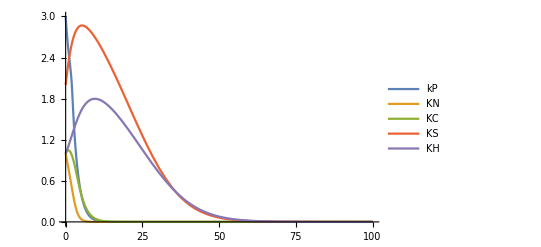

{{5.98954×10^-33,2.45862×10^-43,1.16263×10^-21,0.0000135454,0.000021474}}

```mathematica
(* Results for one set of initial conditions over time *)
tEnd=100;

With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5,I0=0.2,I1=5,J0=0.1,M0=0.1,δS=0.5,η=0.3,γ=0.2,ξ=0.2,α=0.2,δH=0.5},
sol=NDSolve[{
kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)*(KS[t]^η)*(KH[t]^(1-α1-η))-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))*(KS[t]^M0)-δC*KC[t],
KS'[t]==(I0*KS[t]*(I1-KS[t]))*(KC[t]^J0)+(γ*KH[t])-δS*KS[t],
KH'[t]==(ξ*KH[t])+(α*KS[t])-δH*KH[t],
kP[0]==3,KN[0]==1,KC[0]==1,KS[0]==2, KH[0]==1},{kP,KN,KC,KS,KH},{t,0,tEnd},AccuracyGoal->100]]
Plot[Evaluate[{kP[t],KN[t],KC[t],KS[t],KH[t]}/. sol],{t,0,tEnd},PlotRange->All,PlotLegends->{"kP","KN","KC","KS","KH"}]
{kP[tEnd],KN[tEnd],KC[tEnd],KS[tEnd],KH[tEnd]}/.sol
```

```mathematica
tEnd=100;
kPmin=0;
kPmax=15;
KNmin=0;
KNmax=10;
KCmin=0;
KCmax=5;
KSmin = 0;
KSmax = 5;
KHmin=0;
KHmax=5;
stepsize=1;

ListIndices={};
Do[AppendTo[ListIndices,{i,j,k,l,m}],{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize},{l,KSmin,KSmax,stepsize},{m,KHmin,KHmax,stepsize}]
ListSol={};
Do[
With[{A=10,α1=0.4,s1=0.1,s2=0.2,s3=10,d=2,δP=0.5,n=0.5,α2 = 0.4,δN = 1,b=10,H=1.5,c1=1,c2=0.5,q=0.6,T0=0.35,P0=2,PN=2.5,δC=0.5,ρ=0.5,δS=0.5,I0=0.2,I1=5,J0=0.1,M0=0.1,η=0.3,γ=0.2,ξ=0.2,α=0.2,δH=0.5},
sol=NDSolveValue[{
kP'[t]==(s1+(s2-s1)/(1+ⅇ^(-s3*(kP[t]-d))))*(q*(KN[t])^α2)*(A*(kP[t])^α1)*(KS[t]^η)*(KH[t]^(1-α1-η))-(δP+n)*kP[t],
KN'[t]==(T0*KC[t])*((b*(KN[t])^2)/(H^2+(KN[t])^2))*(ρ+(1-ρ)/(1+c1*kP[t]^c2))-δN*KN[t],
KC'[t]==((P0*KN[t])/(PN+KN[t]))*(KS[t]^M0)-δC*KC[t],
KS'[t]==(I0*KS[t]*(I1-KS[t]))*(KC[t]^J0)+(γ*KH[t])-δS*KS[t],
KH'[t]==(ξ*KH[t])+(α*KS[t])-δH*KH[t],
kP[0]==i,KN[0]==j,KC[0]==k,KS[0]==l,KH[0]==m},{kP[tEnd],KN[tEnd],KC[tEnd],KS[tEnd],KH[tEnd]},{t,0,tEnd},AccuracyGoal->50];
AppendTo[ListSol,sol]],
{i,kPmin,kPmax,stepsize},{j,KNmin,KNmax,stepsize},{k,KCmin,KCmax,stepsize},{l,KSmin,KSmax,stepsize},{m,KHmin,KHmax,stepsize}]
AssignClusters=ClusteringComponents[ListSol,Automatic,1,Method-> "GaussianMixture"];
CountDistinct[AssignClusters]
cluster1={};
Do[If[AssignClusters[[m]]==1,AppendTo[cluster1,ListIndices[[m]]]],{m,1,Length[AssignClusters]}]
cluster2={};
Do[If[AssignClusters[[n]]==2,AppendTo[cluster2,ListIndices[[n]]]],{n,1,Length[AssignClusters]}]
cluster3={};
Do[If[AssignClusters[[o]]==3,AppendTo[cluster3,ListIndices[[o]]]],{o,1,Length[AssignClusters]}]

(* Print[ListSol] *)

(* Physical, natural, cultural *)
cluster3pnc=Drop[cluster3,None,{4,5}];
p1=ListPointPlot3D[{cluster3pnc},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,6.7,3.3}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KCmin,KCmax}},
AxesLabel->{"Physical  capital","Natural  capital","Cultural  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Physcial, natural, social  *)
cluster3pns=Drop[cluster3,None,{3,5,2}];
p1=ListPointPlot3D[{cluster3pns},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Natural  capital","Social  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,6.7,3.4}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Natural  capital","Social  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Physcial, natural, human  *)
cluster3pnh=Drop[cluster3,None,{3,4,1}];
p1=ListPointPlot3D[{cluster3pnh},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Natural  capital","Human  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,6.7,2.3}}},
PlotRange->{{kPmin,kPmax},{KNmin,KNmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Natural  capital","Human  capital"},
BoxRatios->{3,2,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Physical, cultural, social *)
cluster3pcs=Drop[cluster3,None,{2,5,3}];
p1=ListPointPlot3D[{cluster3pcs},
PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Cultural  capital","Social  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,3.3,3.4}}},
PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Physical  capital","Cultural  capital","Social  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Physical, cultural, human *)
cluster3pcs=Drop[cluster3,None,{2,4,2}];
p1=ListPointPlot3D[{cluster3pcs},
PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Cultural  capital","Human  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,3.3,2.3}}},
PlotRange->{{kPmin,kPmax},{KCmin,KCmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Cultural  capital","Human  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Natural, cultural, social *)
cluster3ncs=Drop[cluster3,None,{1,5,4}];
p1=ListPointPlot3D[{cluster3ncs},
PlotRange->{{KNmin,KNmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Natural  capital","Cultural  capital","Social  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{6.7,3.3,3.4}}},
PlotRange->{{KNmin,KNmax},{KCmin,KCmax},{KSmin,KSmax}},
AxesLabel->{"Natural  capital","Cultural  capital","Social  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Natural, cultural, human *)
cluster3nch=Drop[cluster3,None,{1,4,3}];
p1=ListPointPlot3D[{cluster3nch},
PlotRange->{{KNmin,KNmax},{KCmin,KCmax},{KHmin,KHmax}},
AxesLabel->{"Natural  capital","Cultural  capital","Human  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{6.7,3.3,2.3}}},
PlotRange->{{KNmin,KNmax},{KCmin,KCmax},{KHmin,KHmax}},
AxesLabel->{"Natural  capital","Cultural  capital","Human  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Physcial, social, human  *)
cluster3psh=Drop[cluster3,None,{2,3,1}];
p1=ListPointPlot3D[{cluster3psh},
PlotRange->{{kPmin,kPmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Social  capital","Human  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{13.2,3.4,2.3}}},
PlotRange->{{kPmin,kPmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Physical  capital","Social  capital","Human  capital"},
BoxRatios->{3,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Natural, social, human *)
cluster3nsh=Drop[cluster3,None,{1,3,2}];
p1=ListPointPlot3D[{cluster3nsh},
PlotRange->{{KNmin,KNmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Natural  capital","Social  capital","Human  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{6.7,3.4,2.3}}},
PlotRange->{{KNmin,KNmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Natural  capital","Social  capital","Human  capital"},
BoxRatios->{2,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* Cultural, social, human *)
cluster3csh=Drop[cluster3,None,{1,2,1}];
p1=ListPointPlot3D[{cluster3csh},
PlotRange->{{KCmin,KCmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Cultural  capital","Social  capital","Human  capital"},
BoxRatios->{1,1,1},
PlotStyle->{Opacity[0.8],PointSize[0.01]}];
p2=ListPointPlot3D[{{{0,0,0},{3.3,3.4,2.3}}},
PlotRange->{{KCmin,KCmax},{KSmin,KSmax},{KHmin,KHmax}},
AxesLabel->{"Cultural  capital","Social  capital","Human  capital"},
BoxRatios->{1,1,1},
PlotStyle->{Red,Opacity[0.8],PointSize[0.05]}];
Show[{p1,p2}]

(* States that can go (depending on non plotted capital) to non poor equilibrium point are plotted as dots. States not plotted as dots always (whatever the value of the non plotted capital is) go to poor equilibrium point. *)
```

3

-Graphics3D-

-Graphics3D-

-Graphics3D-

«7 more identical outputs»